# Variance of Fisher z-transformed quantities

The Fisher z-transform is defined by:

```mathematica
z:=(1/2) Log[(1+x)/(1-x)]
```

where x is the quantity of interest, e.g. a correlation or standardized regression coefficient. It can be seen that the transform maps {x: -1 < 0 <1} → ℝ:

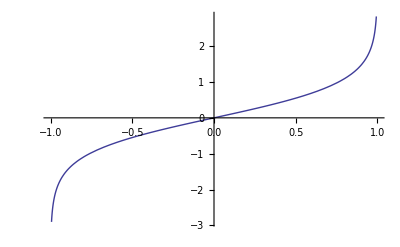

```mathematica
Plot[ArcTanh[x], {x, -1,1}]
```

## Variance of the z-transformed variable

To obtain  asymptotic variance, we require the derivative wrt x:

```mathematica
d=Simplify[D[z,x]]
```

1/(1-x^2)

Then, according to the Delta method, the variance is simply

```mathematica
V d^2
```

V/((1-x^2)^2)

where V is the asymptotic variance of x.

The variance of a correlation coefficient, for example, is approximately

```mathematica
v:= (1-x^2)^2/(n-1)
```

Thus the asymptotic variance of the z-transformed correlation coefficient is

```mathematica
v d^2
```

1/(-1+n)

(Compare this with the unbiased estimator 1/(-3+n))

## Motivation of the z-transform

The z-transform is a transform that removes x from the equation for the variance. You could find this (here cheating by going to the target 1/(n-1)) by solving the differential equation,

```mathematica
Simplify[DSolve[{f'[x]^2v ==1/(n-1), f[0]==0}, f[x], x]]
```

{{f[x]→1/2 (Log[1-x]-Log[1+x])},{f[x]→1/2 (-Log[1-x]+Log[1+x])}}

```mathematica
FullSimplify[%]
```

{{f[x]→-ArcTanh[x]},{f[x]→ArcTanh[x]}}

Unfortunately, this does not work:

```mathematica
Simplify[DSolve[{f'[x]^2v ==g[x],g'[x]==0}, f[x], x]]
```

DSolve::deqx: Supplied equations are not differential equations of the given functions.

DSolve[{((-1+x^2)^2 f'[x]^2)/(-1+n)==g[x],g'[x]==0},f[x],x]

You could also cheat a bit less by specifying “inversely proportional to n” and then minimize the relative variance:

```mathematica
s=FullSimplify[DSolve[{f'[x]^2v ==α + β/(n-1) , f[0]==0}, f[x], x],Assumptions->x^2>1]
```

{{f[x]→√((-1+n) α+β) ArcTanh[x]},{f[x]→-√((-1+n) α+β) ArcTanh[x]}}

The ratio of the value to the variance should be as small as possible:

```mathematica
Simplify[√((-1+n) α+β) ArcTanh[x]/Sqrt[α + β/(n-1)]]
```

(√((-1+n) α+β) ArcTanh[x])/(√(α+β/(-1+n)))

Minimizing with respect to a and b:

```mathematica
Minimize[%,{α,β}]
```

{Piecewise[{{-√(-ArcTanh[x]^2+n ArcTanh[x]^2), ArcTanh[x]≤0&&n>1}, {√(-ArcTanh[x]^2+n ArcTanh[x]^2), ArcTanh[x]>0&&n>1}, {∞, True}}],{α→Piecewise[{{0, (ArcTanh[x]>0&&n>1)||(ArcTanh[x]≤0&&n>1)}, {Indeterminate, True}}],β→Piecewise[{{1, (ArcTanh[x]>0&&n>1)||(ArcTanh[x]≤0&&n>1)}, {Indeterminate, True}}]}}

Thus, so long as n > 1, the best solution is always just 1/(n-1), which would give the ArcTanh.